# Similarity Index of 1D Cellular Automata

## Graph approach

Erick Jesse Angeles Lopez

### Spectral Similarity via Eigenvalue Cosine

Build the transition graph

Turn that graph into an adjacency matrix

Compute the eigenvalues of

Compare two rules with complex cosine distance between their eigenvalue vectors

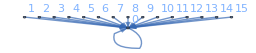
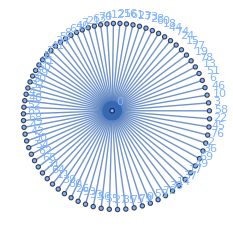
```mathematica
Grid[Transpose[{{,-Graphics-,{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}},{,-Graphics-,{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}}}],Frame->All]
```

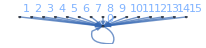
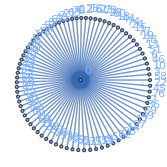
0_(2,3) | 0_(3,3)
-Graphics- | -Graphics-
{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

### Spectral Moments

Instead of comparing the full spectrum, we compare a fixed number of spectral moments:

Run the rule  steps forwards on every possible configuration and define the fraction  of them that landed back exactly where they started.

The new feature vector is:

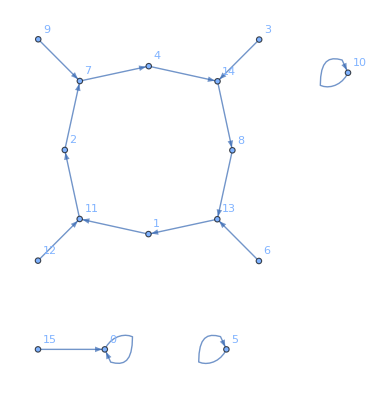
```mathematica
Grid[{{,-Graphics-,<|""->3,""->3,""->3,""->3,""->3,""->3,""->3,""->11|>}},Frame->All]
```

30_(2,3) | -Graphics- | <|→3,→3,→3,→3,→3,→3,→3,→11|>

### Spectral moments similarity

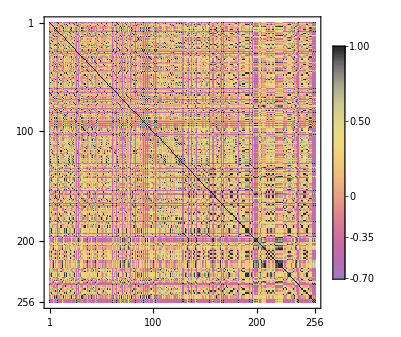
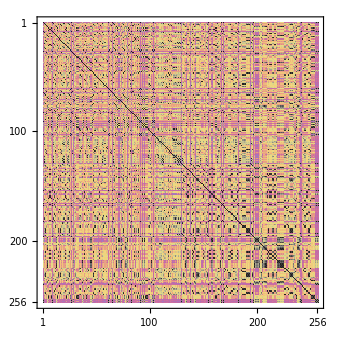
```mathematica
Grid[{{Labeled[-Graphics-,"Eigen Values"],Labeled[-Graphics-,"Spectral moments"]}}]
```

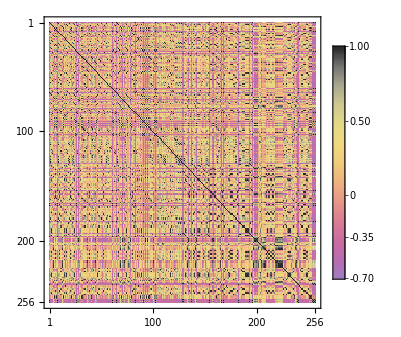
-Graphics-Eigen Values | -Graphics-Spectral moments

### Distance between rules in different spaces

-Graphics-

# Thanks